```mathematica
graph[dat_]:=(


dates=DateList[#]&/@data[[All,12]];
(*Histogram[data[[All,2]]]*)
DateHistogram[dates,"Second",#2*1501&]);
(*result={
{graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode1/mlcnetA.cs.wpi.edu_cubic_0/local.csv","CSV"]],
graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode2/mlcnetA.cs.wpi.edu_cubic_0/local.csv","CSV"]],
graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode3/mlcnetA.cs.wpi.edu_cubic_0/local.csv","CSV"]]},
{graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode1/mlcnetB.cs.wpi.edu_bbr_0/local.csv","CSV"]],
graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode2/mlcnetB.cs.wpi.edu_bbr_0/local.csv","CSV"]],
graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode3/mlcnetB.cs.wpi.edu_bbr_0/local.csv","CSV"]]},
{graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode1/mlcnetC.cs.wpi.edu_hybla_0/local.csv","CSV"]],
graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode2/mlcnetC.cs.wpi.edu_hybla_0/local.csv","CSV"]],
graph[Import["/home/zack/Downloads/data2/2020-11-11/proxyMode3/mlcnetC.cs.wpi.edu_hybla_0/local.csv","CSV"]]}

}*)
```

```mathematica
time=
```

```mathematica
cols
```

```mathematica
Column[{"frame.number","frame.time_epoch","eth.src","eth.dst","ip.src","ip.dst","tcp.srcport","tcp.dstport","tcp.seq","tcp.analysis.ack_rtt","ip.proto","frame.time","frame.len"}]
```

```mathematica
sizes={3,5,10,20,40,100,250};
labels={"bbr","cybic","cubic_hystart_off","hybla"}
$HistoryLength=1;
stepsPerSec=40;
getCountsDir[dir_]:=(
Print["Starting "<>dir];
Run["bash ~/Downloads/tshark.sh "<>dir<>"local.pcap "<>dir<>"redone.csv"];
getCounts[Import[dir<>"redone.csv","CSV"]])
getCountsOld[dat_]:=(
cols=dat[[1]];
data=Drop[dat,1];
SortBy[data,#[[3]]&][[All,3]];
datagroups=GroupBy[data,{#[[5]],#[[6]]}&];
data=Reverse[SortBy[datagroups,Length[#]&]][[1]];
counts=BinCounts[data[[All,2]],1/stepsPerSec]*8*Mean[data[[All,13]]]*(stepsPerSec/1)//N
);
getCounts[dat_]:=(
cols=dat[[1]];
data=Drop[dat,1];
SortBy[data,#[[3]]&][[All,3]];
datagroups=GroupBy[data,{#[[5]],#[[6]]}&];
data=Reverse[SortBy[datagroups,Length[#]&]][[1]];
raw=Table[0,{x,1,Ceiling[stepsPerSec*(Max[data[[All,2]]]-Min[data[[All,2]]])]}];
mindatavalue=Min[data[[All,2]]];
(raw[[ Min[{Ceiling[(#[[2]]-mindatavalue+0.001)*stepsPerSec],Length[raw]}] ]] 
= raw[[Min[{Ceiling[(#[[2]]-mindatavalue+0.001)*stepsPerSec],Length[raw]}]  ]]+8*#[[13]]*stepsPerSec )&/@data;
raw
);

genPlottingData[counts_]:=(
maxLen=Max[Length/@totalCounts];
totalMean=Mean/@Transpose[PadRight[#,maxLen]&/@totalCounts];
totalStddev=StandardDeviation/@Transpose[PadRight[#,maxLen]&/@totalCounts];
totalVal=Around[#[[1]],#[[2]]]&/@Transpose[{totalMean,totalStddev}];
plottingData=Transpose[{Table[x/stepsPerSec,{x,0,maxLen-1}]//N,totalVal}];
plottingData
)
bruteOutputLastTerm[protocol_,size_,computer_]:=(
totalCounts={getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_0/"],
getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_1/"],
getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_2/"],
getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_3/"],
getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_4/"]};
plottingData=genPlottingData[totalCounts]
)
bruteOutput[protocol_,size_,delay_,computer_]:=(
totalCounts={
getCountsDir["~/Downloads/2020-12-14/"<>size<>"/"<>ToString[delay]<>"/"<>computer<>"_0/"],
getCountsDir["~/Downloads/2020-12-14/"<>size<>"/"<>ToString[delay]<>"/"<>computer<>"_1/"],
getCountsDir["~/Downloads/2020-12-14/"<>size<>"/"<>ToString[delay]<>"/"<>computer<>"_2/"],
getCountsDir["~/Downloads/2020-12-14/"<>size<>"/"<>ToString[delay]<>"/"<>computer<>"_3/"],
getCountsDir["~/Downloads/2020-12-14/"<>size<>"/"<>ToString[delay]<>"/"<>computer<>"_4/"],
getCountsDir["~/Downloads/2020-12-14/"<>size<>"/"<>ToString[delay]<>"/"<>computer<>"_5/"],
getCountsDir["~/Downloads/2020-12-14/"<>size<>"/"<>ToString[delay]<>"/"<>computer<>"_6/"]};
totalCounts=Select[totalCounts,Length[#]≠0&];
totalCounts=Drop[#,FirstPosition[#,Drop[Select[#,#≠0&,2],1][[1]]][[1]]]&/@totalCounts;
plottingData=genPlottingData[totalCounts]
)
(*plottingData=bruteOutput[ToString[#],"mlcnetA.cs.wpi.edu_cubic"]&/@{3,5,10,20,40,100,250};*)
fullData={
bruteOutput["cubic",ToString[#],16,"mlcnetD.cs.wpi.edu_cubic"]&/@sizes,
bruteOutput["cubic",ToString[#],32,"mlcnetD.cs.wpi.edu_cubic"]&/@sizes
(*bruteOutput["cubic_hystart_off",ToString[#],"mlcnetA.cs.wpi.edu_cubic_hystart_off"]&/@{3,5,10,20,40,100,250},
bruteOutput["cubic",ToString[#],"mlcnetA.cs.wpi.edu_cubic"]&/@{3,5,10,20,40,100,250},
bruteOutput["hybla",ToString[#],"mlcnetC.cs.wpi.edu_hybla"]&/@{3,5,10,20,40,100,250}*)

};

bruteOutputLastTerm[protocol_,size_,computer_]:=(
totalCounts={getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_0/"],
getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_1/"],
getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_2/"],
getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_3/"],
getCountsDir["~/Downloads/last_term/initcwnd_experiments/"<>protocol<>"/"<>size<>"/"<>computer<>"_4/"]};
plottingData=genPlottingData[totalCounts]
)
```

{bbr,cybic,cubic_hystart_off,hybla}

Starting ~/Downloads/2020-12-14/3/16/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/3/16/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/3/16/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/3/16/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/3/16/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/3/16/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/3/16/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/5/16/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/5/16/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/5/16/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/5/16/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/5/16/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/5/16/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/5/16/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/10/16/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/10/16/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/10/16/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/10/16/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/10/16/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/10/16/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/10/16/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/20/16/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/20/16/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/20/16/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/20/16/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/20/16/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/20/16/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/20/16/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/40/16/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/40/16/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/40/16/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/40/16/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/40/16/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/40/16/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/40/16/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/100/16/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/100/16/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/100/16/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/100/16/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/100/16/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/100/16/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/100/16/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/250/16/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/250/16/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/250/16/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/250/16/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/250/16/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/250/16/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/250/16/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/3/32/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/3/32/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/3/32/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/3/32/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/3/32/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/3/32/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/3/32/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/5/32/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/5/32/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/5/32/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/5/32/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/5/32/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/5/32/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/5/32/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/10/32/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/10/32/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/10/32/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/10/32/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/10/32/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/10/32/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/10/32/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/20/32/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/20/32/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/20/32/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/20/32/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/20/32/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/20/32/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/20/32/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/40/32/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/40/32/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/40/32/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/40/32/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/40/32/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/40/32/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/40/32/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/100/32/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/100/32/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/100/32/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/100/32/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/100/32/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/100/32/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/100/32/mlcnetD.cs.wpi.edu_cubic_6/

Starting ~/Downloads/2020-12-14/250/32/mlcnetD.cs.wpi.edu_cubic_0/

Starting ~/Downloads/2020-12-14/250/32/mlcnetD.cs.wpi.edu_cubic_1/

Starting ~/Downloads/2020-12-14/250/32/mlcnetD.cs.wpi.edu_cubic_2/

Starting ~/Downloads/2020-12-14/250/32/mlcnetD.cs.wpi.edu_cubic_3/

Starting ~/Downloads/2020-12-14/250/32/mlcnetD.cs.wpi.edu_cubic_4/

Starting ~/Downloads/2020-12-14/250/32/mlcnetD.cs.wpi.edu_cubic_5/

Starting ~/Downloads/2020-12-14/250/32/mlcnetD.cs.wpi.edu_cubic_6/

```mathematica
|
```

```mathematica
fullData[[1,2]]//Length
```

```mathematica
fullDataThisTerm=fullData
stepsPerSec=3;
fullDataLastTerm={
bruteOutputLastTerm["bbr",ToString[#],"mlcnetB.cs.wpi.edu_bbr"]&/@{3,5,10,20,40,100,250},
bruteOutputLastTerm["cubic_hystart_off",ToString[#],"mlcnetA.cs.wpi.edu_cubic_hystart_off"]&/@{3,5,10,20,40,100,250},
bruteOutputLastTerm["cubic",ToString[#],"mlcnetA.cs.wpi.edu_cubic"]&/@{3,5,10,20,40,100,250},
bruteOutputLastTerm["hybla",ToString[#],"mlcnetC.cs.wpi.edu_hybla"]&/@{3,5,10,20,40,100,250}

};
```

10

Take::take: Cannot take positions 1 through 400 in {{0.,2.6},{0.025,1.2},{0.05,1.24},{0.075,2.7},{0.1,1.9},{0.125,3.1},«39»,{1.125,4.9},{1.15,4.6},{1.175,5.5},{1.2,5.3},{1.225,6.0},«158»}.

Take::take: Cannot take positions 1 through 400 in {{0.,23680},{0.025,1.22},{0.05,1.5},{0.075,3.0},{0.1,1.9},{0.125,3.6},«39»,{1.125,5.0},{1.15,5.1},{1.175,5.8},{1.2,5.8},{1.225,6.6},«154»}.

Take::take: Cannot take positions 1 through 400 in {{0.,2.6},{0.025,1.1},{0.05,1.5},{0.075,3.2},{0.1,2.3},{0.125,3.7},«39»,{1.125,5.8},{1.15,5.5},{1.175,6.6},{1.2,6.1},{1.225,7.2},«153»}.

General::stop: Further output of Take::take will be suppressed during this calculation.

Part::partw: Part 400 of {{0.,2.6},{0.025,1.2},{0.05,1.24},{0.075,2.7},{0.1,1.9},{0.125,3.1},«39»,{1.125,4.9},{1.15,4.6},{1.175,5.5},{1.2,5.3},{1.225,6.0},«158»} does not exist.

Part::partd: Part specification {{0.,2.6},{0.025,1.2},{0.05,1.24},{0.075,2.7},{0.1,1.9},{0.125,3.1},«39»,{1.125,4.9},{1.15,4.6},{1.175,5.5},{1.2,5.3},{1.225,6.0},«158»}⟦400⟧⟦2,1⟧ is longer than depth of object.

Part::partw: Part 400 of {{0.,23680},{0.025,1.22},{0.05,1.5},{0.075,3.0},{0.1,1.9},{0.125,3.6},«39»,{1.125,5.0},{1.15,5.1},{1.175,5.8},{1.2,5.8},{1.225,6.6},«154»} does not exist.

Part::partd: Part specification {{0.,23680},{0.025,1.22},{0.05,1.5},{0.075,3.0},{0.1,1.9},{0.125,3.6},«39»,{1.125,5.0},{1.15,5.1},{1.175,5.8},{1.2,5.8},{1.225,6.6},«154»}⟦400⟧⟦2,1⟧ is longer than depth of object.

Part::partw: Part 400 of {{0.,2.6},{0.025,1.1},{0.05,1.5},{0.075,3.2},{0.1,2.3},{0.125,3.7},«39»,{1.125,5.8},{1.15,5.5},{1.175,6.6},{1.2,6.1},{1.225,7.2},«153»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {{0.,2.6},{0.025,1.1},{0.05,1.5},{0.075,3.2},{0.1,2.3},{0.125,3.7},«39»,{1.125,5.8},{1.15,5.5},{1.175,6.6},{1.2,6.1},{1.225,7.2},«153»}⟦400⟧⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{0,10},{0,Max[«1»]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{0,10},{0,Max[{{0.,0},{0.025,0},{0.05,21120},{0.075,42560},{0.1,Around[«2»]},{0.125,Around[«2»]},{0.15,Around[«2»]},«38»,{1.125,Around[«2»]},{1.15,Around[«2»]},{1.175,Around[«2»]},{1.2,Around[«2»]},{1.225,Around[«2»]},«162»}⟦400⟧⟦2,1⟧,«1»,«4»,«1»]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

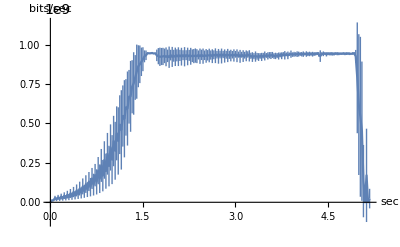
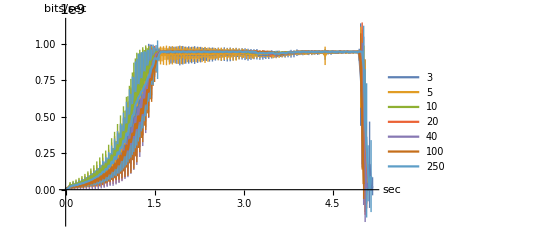
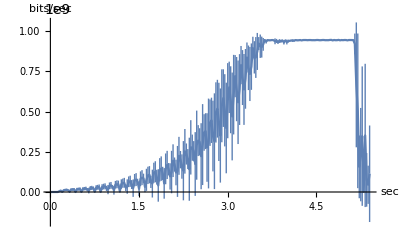
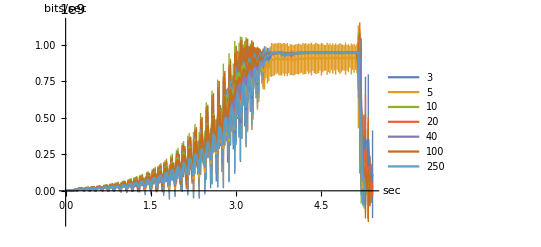
bbr | cybic | cubic_hystart_off | hybla
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics- |  |

```mathematica
sizes={3,5,10,20,40,100,250,5000};
timeIntervalPlot=10
plot[plottingData_]:=({ListLinePlot[plottingData[[1]],AxesLabel->{"sec","bits/sec"}],
ListLinePlot[plottingData,PlotLegends->sizes,AxesLabel->{"sec","bits/sec"}],
ListLinePlot[Take[#,timeIntervalPlot*stepsPerSec]&/@plottingData,PlotLegends->sizes,AxesLabel->{"sec","bits/sec"},PlotRange->{{0,timeIntervalPlot},{0,Max[#[[timeIntervalPlot*stepsPerSec]][[2,1]]&/@plottingData]}}]});
plots=plot/@fullData;
TableForm[{labels,plots}]
```

```mathematica
data=getCountsDir["~/Downloads/last_term/initcwnd_experiments/cubic"];
data//Length
ListLinePlot[Transpose[{Table[x/stepsPerSec,{x,0,Length[data]-1}]//N,data}],AxesLabel->{"sec","bits/sec"},PlotLabel->"Throughput vs Time cubic hystart off. Trial 1 cwnd=40"]

fullData//Dimensions
```

```mathematica
Take[#,10]//Length
```

```mathematica
sizes={3,5,10,20,40,100,250};
timeIntervalPlot=1
plot[plottingData_]:=({(*ListLinePlot[plottingData[[5]],AxesLabel->{"sec","bits/sec"}],
ListLinePlot[plottingData,PlotLegends->sizes,AxesLabel->{"sec","bits/sec"}],*)
ListLinePlot[Take[#,timeIntervalPlot*stepsPerSec]&/@plottingData,PlotLegends->sizes,AxesLabel->{"sec","bits/sec"},PlotRange->{{0,timeIntervalPlot},{0,Max[#[[timeIntervalPlot*stepsPerSec]][[2,1]]&/@plottingData]}}]});
plots=plot/@fullData;
TableForm[{labels,plots}]
```

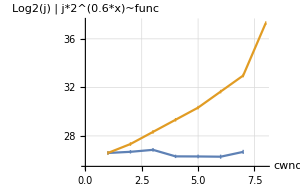
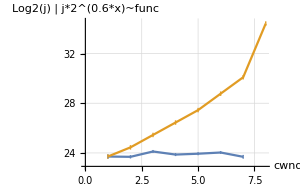
bbr | cybic | cubic_hystart_off | hybla
-Graphics- | -Graphics- |  |

{3,5,10,20,40,100,250,5000}

```mathematica
genDiff[plottingData_]:=(
caluculatedShifts=(
equation=Fit[Take[#,1*stepsPerSec],{2^(x*(28/1000))},x,"BestFit"];
intercept=equation/.{x->0};
shift=Log[intercept]/Log[2]
)&/@plottingData;
shifts=Log[#]/Log[2]&/@sizes//N;
(*shifts=shifts/2;*)
shifts=shifts-shifts[[1]];
shifted=shifts+caluculatedShifts[[1]];

ListLinePlot[{caluculatedShifts,shifted},GridLines->Automatic,AxesLabel->{"cwnd","Log2(j) | j*2^(0.6*x)~func"},ImageSize->300]);
diffGraphs=genDiff/@fullData;
TableForm[{labels,diffGraphs}]
sizes
```

```mathematica
Show[diffGraphs]
```

```mathematica
zeroShiftSet[set_]:=(
(*First position where the throughput is non-zero*)
firstNonZero=Select[set,#[[2]]["Value"]≠0&,1];
newset=#-{firstNonZero[[1,1]],0}&/@set;
Select[newset,#[[1]]>0&]
);
zeroShiftDataset[largeData_]:=(
zeroShiftSet/@largeData
)
fullData=zeroShiftDataset/@fullDataSave
```

```mathematica
Select[newset,#[[1]]>0&]
```

```mathematica
fullDataSave=fullData
```

```mathematica
{1,2}-{1,0}
```

```mathematica
Show[{ListLinePlot[fullData[[2,4]]],Plot[2^(x*0.6+16.5),{x,0,20},PlotStyle->Red],Plot[2^(x*0.6+17.1),{x,0,20},PlotStyle->Black]}]
```

```mathematica
$HistoryLength=1
```

```mathematica
2^23
```

```mathematica
ListLinePlot[counts]
```

```mathematica
dat=Import["/home/zack/Downloads/last_term/initcwnd_experiments/cubic/20/mlcnetA.cs.wpi.edu_cubic_0/redone.csv"]
```

```mathematica
caluculatedShifts=(
equation=Fit[Take[#,10*stepsPerSec],{2^(x*0.6)},x,"BestFit"];
intercept=equation/.{x->0};
shift=Log[intercept]/Log[2]
)&/@fullData[[2]]
equation
```

```mathematica
sizesDJ=(DeleteDuplicates[djTrump[[All,#]]]//Length)&/@Table[x,{x,1,Length[djTrump[[1]]]}]
```

```mathematica
TableForm[{djTrump[[1]],sizesDJ}//Transpose]
```

```mathematica
latlong=Select[djTrump[[All,{14,15}]],NumberQ[#[[1]]]&&NumberQ[#[[2]]]&];
coords=CountryData["UnitedStates","Coordinates"];
Graphics[{Red,Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"][[1]]&,{latlong},{2}],Gray,Polygon[Map[GeoGridPosition[GeoPosition[#],"Mercator"][[1]]&,CountryData[#,"Coordinates"],{2}]]&/@CountryData["Countries"]}]
```

```mathematica
Length@positions
```

```mathematica
Graphics[{Gray,Polygon[Map[GeoGridPosition[GeoPosition[#],"Mercator"][[1]]&,CountryData["UnitedStates","Coordinates"],{2}]],Red,PointSize[.02],Point/@Map[GeoGridPosition[GeoPosition[#],"Mercator"][[1]]&,{latlong},{2}]}]
```

```mathematica
Graphics[{EdgeForm[Black],Polygon[Reverse/@First[coords]],Red,Point/@Reverse/@latlong}]
```

```mathematica
GeoGraphics[{Red,PointSize[.002],Point@GeoPosition@latlong},GeoRange->"World",GeoProjection->"Mollweide",GeoGridLines->Quantity[5,"AngularDegrees"],GeoBackground->"ContourMap"]
```